```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ryanplestid/Research/Physics_Projects/Archived_Projects/Public/Solar-Upscatter/Mathematica/Paper-I-clean

```mathematica
PrettyExp[x_,MAX_: 2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
fticksR[min_,max_,AMAX_: 1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
fticksRevens[min_,max_,AMAX_: 1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,If[Mod[x,2]==0,PrettyExp[x,AMAX],""],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]

ourTicksPrettify[{minY_,maxY_},{minX_,maxX_}, notationThreshold_]:= {{fticksRevens[10^(minY),10^(maxY),notationThreshold],None},{fticksR[10^(minX),10^(maxX),notationThreshold],None}};
```

```mathematica
exclCurves=Import["Exclusion-Curves/exclCurves.m"];
rescale={#⟦1⟧,1.97 10^-9#⟦2⟧}&;
Do[
Do[
Do[
exclCurves[expt][shape][flav]=rescale/@exclCurves[expt][shape][flav],{flav,Keys@exclCurves[expt][shape]}
 ],
{shape, Keys@exclCurves[expt]} 
 ]
,{expt,Keys@exclCurves}
]
thisWorkBox=Join[{{0.01,1.12 1.97 10^-9}},Table[{mN,Min[Table[Interpolation[exclCurves[expt]["Box"]["μ"],InterpolationOrder->2][mN] ,{expt,Keys@exclCurves}]]},{mN,0.05,18.7,0.01}]//Quiet];
```

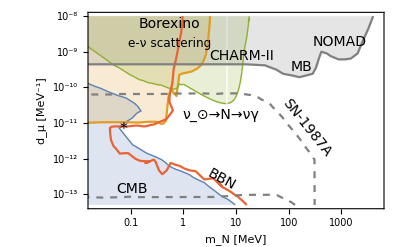

```mathematica
p1=ListLogLogPlot[{({#⟦1⟧,1/6.75^2#⟦2⟧}&)/@Import["Existing-Limits/CMB.csv"],
({#⟦1⟧,1/6.75^2#⟦2⟧}&)/@Import["Existing-Limits/Borexino-Elastic.csv"],thisWorkBox,
({#⟦1⟧,1/6.75^2#⟦2⟧}&)/@Import["Existing-Limits/BBN.csv"],({#⟦1⟧,#⟦2⟧}&)/@Import["Existing-Limits/MB-NOMAD-LEP.csv"],({#⟦1⟧,1/6.75^2#⟦2⟧}&)/@Import["Existing-Limits/SN1987A.csv"]},Joined->True,Frame->True,PlotRangePadding->0,FrameTicks->ourTicksPrettify[{-13.5,-8},{-2,3},2],PlotRange->{{0.02,5000},{5 10^-14, 10^-8}},PlotStyle->{{Automatic,Thin},{Automatic},{Thick,{ColorData[97,3],Lighter}},{ColorData[97,4]},{Gray},{Dashed,Gray}},
Epilog-> {Inset[Style["*",16],{Log[0.0745],Log[1/6.75^2 2.99 10^-10]}],Inset[Style["NOMAD",14],Scaled[{0.85,0.85}]],Inset[Style["MB",14],Scaled[{0.72,0.72}]],Inset[Style["CHARM-II",14],Scaled[{0.52,0.78}]],
Inset[Style["CMB",14],Scaled[{0.15,0.1}]],
Inset[Style["Borexino",14],Scaled[{0.275,0.94}]],
Inset[Style["e-ν scattering",12],Scaled[{0.275,0.84}]],
Inset[Style["ν_⊙→N→νγ",14],Scaled[{0.45,0.475}]],
Inset[Rotate[Style["SN-1987A",14],-0.9],Scaled[{0.74,0.41}]],
Inset[Rotate[Style["BBN",14],-0.5],Scaled[{0.45,0.15}]]},Filling->{1-> Bottom,2->Top,3-> Top,5-> Top},FrameStyle->Black,FrameLabel->(Style[#,12]&)/@{"m_N       [MeV]", "d_μ      [MeV^-1]"}
]
```

```mathematica
Export["PDFs/Comparison-Plot.pdf",p1];
```